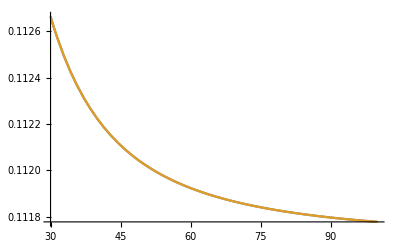

```mathematica
δ[n_,δ0_,δ2_,δ4_]:=δ0+δ2/(n-δ0)^2+δ4/(n-δ0)^4;
n1[n_]:=n-δ[n,3.26896,-0.138,0.9];
n2[n_]:=(n+1)-δ[n+1,3.371,0.5,-10];
Plot[{Abs[-2(n1[n]n2[n])^(1/2)/(n1[n]+n2[n])Sin[π(n2[n]-n1[n])]/(π(n2[n]-n1[n]))],Abs[-2(n2[n]n1[n])^(1/2)/(n2[n]+n1[n])Sin[π(n1[n]-n2[n])]/(π(n1[n]-n2[n]))]},{n,30,100}]
```